# Introduction to Computational Physical Chemistry

© 2017 by Joshua Schrier and University Science Books  (Version: 25 July 2017)
Publisher’s Website: http://www.uscibooks.com/schrier.htm

## Chapter 14 - Molecular Dynamics

## 14.2 INITIALIZATION

```mathematica
initPositions[nParticles_,boxLength_]:=Module[
{coords={},perSide=Ceiling[Sqrt[nParticles]]},Do[ (*loop over lattice points*)If[Length[coords]<nParticles,AppendTo[coords,{i,j}*((boxLength)/perSide)-0.5] ];
,{i,1,perSide},{j,1,perSide}
];
N[coords] (*return list of coordinates*)
];
```

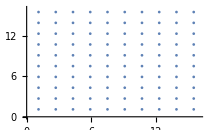

```mathematica
ListPlot[ initPositions[100,16],PlotRange->{{0,16},{0,16}}]
```

```mathematica
initVelocities[temperature_,coords_,dt_]:=Module[
{nParticles,nFreedom,velocities,sumV,scale,v2},
nParticles=Length[coords];
nFreedom=2*nParticles-2;
(*assign random velocities; this is not a Boltzmann distribution!*)
velocities=RandomReal[{-0.5,+0.5},{nParticles,2}];

(*remove center-of-mass motion of the system*)
sumV=Total[velocities]/nParticles;Do[velocities[[i]]-=sumV,{i,1,nParticles}];

(*compute kinetic energy and rescale velocity to match temperature*)v2=Sum[Norm[velocities[[i]]]^2,{i,1,nParticles}];scale=Sqrt[nFreedom*temperature/v2];
velocities*=scale;(*rescale to obtain desired temperature*)

(coords-velocities*dt) (*return positions at previous timestep*)
];
```

```mathematica
coords=initPositions[100,16];
prevCoords=initVelocities[1,coords,0.001];
```

```mathematica
Total[ velocities=(coords-prevCoords)/0.001 ]
```

{-5.10703×10^-12,6.21725×10^-12}

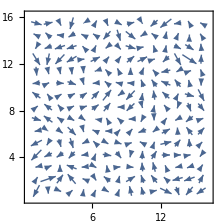

```mathematica
ListVectorPlot[ Partition[ Riffle[coords,velocities], 2] ]
```

## 14.3 COMPUTING THE FORCE

### 14.3.1 Lennard-Jones potential

```mathematica
energyLJ[r_,sigma_,epsilon_]:=4.*epsilon*((sigma/r)^12-(sigma/r)^6)
```

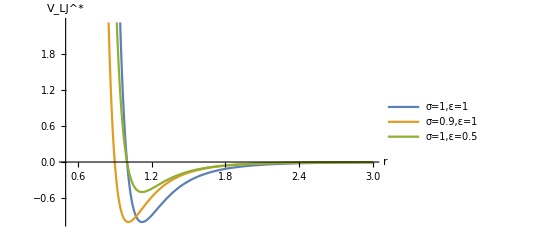

```mathematica
Plot[
{energyLJ[r,1,1],energyLJ[r,0.9,1],energyLJ[r,1,0.5]},{r,0.5,3},AxesLabel->{"r","V_LJ^*"},PlotLegends->{"σ=1,ε=1","σ=0.9,ε=1","σ=1,ε=0.5"}]
```

```mathematica
energyLJ[r_]:=4.*(r^-12-r^-6);
```

```mathematica
energyLJ[r_,rc_]:=If[r<rc,energyLJ[r]-energyLJ[rc],0];
```

### 14.3.2 Lennard-Jones force

```mathematica
computeForces[coords_,boxLength_,rCut_]:=Module[
{nParticles,forces,distVec,dist,pairwiseForce},
nParticles=Length[coords];forces=Table[{0.,0.},{nParticles}];
Do[ (*loop over unique pairs of particles*)
distVec=coords[[i]]-coords[[j]];(*calculate distance*)
(*apply minimum image convention to x and y vector components*)distVec[[1]]-=boxLength*Round[distVec[[1]]/boxLength];distVec[[2]]-=boxLength*Round[distVec[[2]]/boxLength];dist=Norm[distVec];
If[dist≤rCut,(*evaluate truncated-shifted LJ force*)pairwiseForce=(48.*dist^-14)-(24.*dist^-8);forces[[i]]+=pairwiseForce*distVec;forces[[j]]-=pairwiseForce*distVec;
];
,{i,1,nParticles-1},{j,i+1,nParticles}];
forces (*return final list of forces on each particle*)
];
```

## 14.4 INTEGRATING NEWTON’S EQUATION OF MOTION

### 14.4.1 Verlet algorithm

```mathematica
integrateEOM[coords_,prevCoords_,forces_,dt_,boxLength_]:=Module[
{newCoords},
newCoords=2.*coords-prevCoords+dt^2*forces;(*Verlet*)
newCoords=Mod[newCoords,boxLength];(*enforce PBC*)
{newCoords,coords}
];
```

### 14.4.2 Running the simulation

```mathematica
(*initialize and define simulation parameters*)
nParticles=100; boxLength=16.;density=nParticles/boxLength^2; 
rCut=2.5;
dt=0.01; 
temperature=1.;
totalTime=0.;

coords=initPositions[nParticles,boxLength];
prevCoords=initVelocities[temperature,coords,dt];

coordMovie={};

AppendTo[coordMovie,
ListPlot[coords,PlotRange->{{0,boxLength},{0,boxLength}}]];

Do[ (*loop over updates*)
totalTime+=dt;(*increment time counter*)
forces=computeForces[coords,boxLength,rCut];(*calc.force and EOM*)
{coords,prevCoords}=integrateEOM[coords,prevCoords,forces,dt,boxLength];
AppendTo[coordMovie,(*animate results*)ListPlot[coords,PlotRange->{{0,boxLength},{0,boxLength}}]];
,{500} (*repeat 500 times*)
];

ListAnimate[ coordMovie,{50}]  (*generate animation*)
```

## 14.5 ADVANCED MATHEMATICA: COMPILED FUNCTIONS

```mathematica
Timing[
Do[
totalTime+=dt;
forces=computeForces[coords,boxLength,rCut];
{coords,prevCoords}=integrateEOM[coords,prevCoords,forces,dt,boxLength];
,{500}];
]
```

{51.0186,Null}

```mathematica
ccomputeForces=Compile[
{{coords,_Real,2},{boxLength,_Real},{rCut,_Real}},
Module[(*unmodified...*)
{nParticles,forces,distVec,dist,pairwiseForce},
nParticles=Length[coords];
forces=Table[{0.,0.},{nParticles}];
Do[ (*loop over unique pairs of particles*)
distVec=coords[[i]]-coords[[j]];(*calculate distance*)

(*apply minimum image convention to x and y vector components*)distVec[[1]]-=boxLength*Round[distVec[[1]]/boxLength];distVec[[2]]-=boxLength*Round[distVec[[2]]/boxLength];dist=Norm[distVec];

If[dist≤rCut,(*evaluate truncated-shifted LJ force*)pairwiseForce=(48.*dist^-14)-(24.*dist^-8);forces[[i]]+=pairwiseForce*distVec;forces[[j]]-=pairwiseForce*distVec;
];
,{i,1,nParticles-1},{j,i+1,nParticles}];
forces (*return final list of forces on each particle*)
]]; (*<--remember to add extra] for Compile[]*)

cintegrateEOM=Compile[
{{coords,_Real,2},{prevCoords,_Real,2},{forces,_Real,2},{dt,_Real},{boxLength,_Real}},
Module[{newCoords},(*unmodified...*)
newCoords=2.*coords-prevCoords+dt^2*forces;(*Verlet*)
newCoords=Mod[newCoords,boxLength];(*enforce PBC*)
{newCoords,coords}
]]; (*<--remember to add extra] for Compile[]*)
```

```mathematica
Timing[
Do[
totalTime+=dt;
forces=ccomputeForces[coords,boxLength,rCut];
{coords,prevCoords}=cintegrateEOM[coords,prevCoords,forces,dt,boxLength];
,{500}
];
]
```

{2.94826,Null}

```mathematica
Needs["CCompilerDriver`"]
CCompilers[]
```

CCompilers::shdw: Symbol CCompilers appears in multiple contexts {CCompilerDriver`,Global`}; definitions in context CCompilerDriver` may shadow or be shadowed by other definitions.

{{Name→Clang,Compiler→CCompilerDriver`ClangCompiler`ClangCompiler,CompilerInstallation→/usr/bin,CompilerName→Automatic},{Name→GCC,Compiler→CCompilerDriver`GCCCompiler`GCCCompiler,CompilerInstallation→/usr/bin,CompilerName→Automatic}}

```mathematica
ccomputeForces=Compile[
{{coords,_Real,2},{boxLength,_Real},{rCut,_Real}},
Module[ (*unmodified...*)
{nParticles,forces,distVec,dist,pairwiseForce},
nParticles=Length[coords];forces=Table[{0.,0.},{nParticles}];
Do[ (*loop over unique pairs of particles*)
distVec=coords[[i]]-coords[[j]];(*calculate distance*)
(*apply minimum image convention to x and y vector components*)distVec[[1]]-=boxLength*Round[distVec[[1]]/boxLength];distVec[[2]]-=boxLength*Round[distVec[[2]]/boxLength];dist=Norm[distVec];

If[dist≤rCut,(*evaluate truncated-shifted LJ force*)pairwiseForce=(48.*dist^-14)-(24.*dist^-8);forces[[i]]+=pairwiseForce*distVec;forces[[j]]-=pairwiseForce*distVec;
];
,{i,1,nParticles-1},{j,i+1,nParticles}];
forces (*return final list of forces on each particle*)
],CompilationTarget->"C"];(*<--only modification*)

cintegrateEOM=Compile[
{{coords,_Real,2},{prevCoords,_Real,2},{forces,_Real,2},{dt,_Real},{boxLength,_Real}},
Module[{newCoords},(*unmodified...*)
newCoords=2.*coords-prevCoords+dt^2*forces;(*Verlet*)
newCoords=Mod[newCoords,boxLength];(*enforce PBC*)
{newCoords,coords}
],CompilationTarget->"C"];(*<--only modification*)
```

```mathematica
Timing[
Do[
totalTime+=dt;
forces=ccomputeForces[coords,boxLength,rCut];
{coords,prevCoords}=cintegrateEOM[coords,prevCoords,forces,dt,boxLength];
,{500}
];
]
```

{0.665215,Null}

## 14.6 SAMPLING THERMODYNAMIC DATA

```mathematica
cCalcPE=Compile[{{coords,_Real,2},{boxLength,_Real},{rCut,_Real}},Module[{nParticles,distVec,dist,PE=0.,Ecut=4.*(rCut^-12-rCut^-6)},nParticles=Length[coords];
Do[ (*loop over unique pairs of particles*)
distVec=coords[[i]]-coords[[j]];distVec[[1]]-=boxLength*Round[distVec[[1]]/boxLength];distVec[[2]]-=boxLength*Round[distVec[[2]]/boxLength];dist=Norm[distVec]; (*calculate distance*)
If[dist≤rCut,(*evaluate truncated-shifted LJ potential*)PE+=4.*(dist^-12-dist^-6)-Ecut;
];
,{i,1,nParticles-1},{j,i+1,nParticles}];
PE (*return total value of potential energy*)
],CompilationTarget->"C"];
```

```mathematica
cCalcKE=Compile[
{{coords,_Real,2},{prevCoords,_Real,2},{dt,_Real},{boxLength,_Real}},Module[
{dx,KE=0.},(*initialize variables*)
Do[ (*loop over all particles*)
dx=coords[[i]]-prevCoords[[i]];(*finite difference*)
dx[[1]]-=boxLength*Round[dx[[1]]/boxLength];dx[[2]]-=boxLength*Round[dx[[2]]/boxLength];KE+=0.5*(Norm[dx]/dt)^2;(*accumulate total kinetic energy*)
,{i,1,Length[coords]}
];
KE (*return total kinetic energy*)
],CompilationTarget->"C"];
```

```mathematica
runSimulation[nParticles_,boxLength_,rCut_,dt_,temperature_,nEquil_,nRun_,nSample_,nSampleCoords_]:=Module[
{coords,prevCoords,forces,PElist={},KElist={},TElist={},coordList={}},

coords=initPositions[nParticles,boxLength];
prevCoords=initVelocities[temperature,coords,dt];

Do[ (*perform equilibration*)
forces=ccomputeForces[coords,boxLength,rCut];{coords,prevCoords}=
cintegrateEOM[coords,prevCoords,forces,dt,boxLength];
,{nEquil}];
Do[ (*perform data-gathering part of simulation*)forces=ccomputeForces[coords,boxLength,rCut];{coords,prevCoords}=
cintegrateEOM[coords,prevCoords,forces,dt,boxLength];If[ Mod[totalTime,nSample]==0,(*collect data every nSample steps*)AppendTo[PElist,{totalTime*dt,cCalcPE[coords,boxLength,rCut]}];AppendTo[KElist,
{totalTime*dt,cCalcKE[coords,prevCoords,dt,boxLength]}];AppendTo[TElist,{totalTime*dt,PElist[[-1,2]]+KElist[[-1,2]]}];
];

If[Mod[totalTime,nSampleCoords]==0,(*collect coord sample*)AppendTo[coordList,{totalTime*dt,coords}];
];
,{totalTime,nRun}];

{PElist,KElist,TElist,coordList} (*return collected samples*)
];
```

```mathematica
{PElist16,KElist16,TElist16,coordList16}=runSimulation[100,16.,2.5,0.0005,1.5,500,5000,50,100];
{PElist11,KElist11,TElist11,coordList11}=runSimulation[100,11.,2.5,0.0005,1.5,500,5000,50,100];
{PElist9,KElist9,TElist9,coordList9}=runSimulation[100,9.,2.5,0.0005,1.5,500,5000,50,100];
```

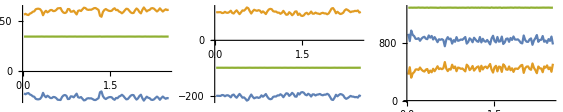

```mathematica
GraphicsGrid[{{ListPlot[{PElist16,KElist16,TElist16},Joined->True,PlotMarkers->None],ListPlot[{PElist11,KElist11,TElist11},Joined->True,PlotMarkers->None],ListPlot[{PElist9,KElist9,TElist9},Joined->True,PlotMarkers->None]}}]
```

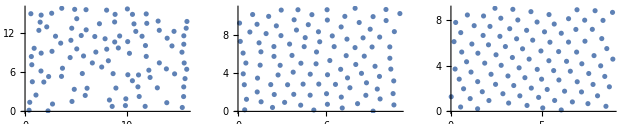

```mathematica
GraphicsGrid[
{{ListPlot[coordList16[[-1,2]]],
ListPlot[coordList11[[-1,2]]],
ListPlot[coordList9[[-1,2]]]}}]
```

### 14.6.1 Radial distribution function

```mathematica
calcDistances=Compile[{{coords,_Real,2},{boxLength,_Real}},
Module[
{nParticles=Length[coords],distList={},dist,distVec},Do[ (*loop over unique pairs*)
distVec=coords[[i]]-coords[[j]];(*calculate distance*)
distVec[[1]]-=boxLength*Round[distVec[[1]]/boxLength];distVec[[2]]-=boxLength*Round[distVec[[2]]/boxLength];dist=Norm[distVec];
If[dist<boxLength/2,AppendTo[distList,dist]];
,{i,nParticles-1},{j,i+1,nParticles}];
distList
],CompilationTarget->"C"];
```

```mathematica
calcGr[coordList_,boxLength_,dr_]:=Module[
{distList={},density=Length[coordList[[1,2]]]/(boxLength^2),nSample,gr},Do[ (*loop over different time snapshots of the coordinates*)distList=Join[distList,calcDistances[coordList[[t,2]],boxLength]];
,{t,Length[coordList]}];nSample=0.5*Length[coordList[[1,2]]]*Length[coordList];gr=BinCounts[distList,dr];

distList=Table[Ceiling[Min[distList]-dr,dr]+(i-1)*dr,{i,Length[gr]}];Do[(*loop over each bin of g(r) values*)gr[[i]]/=(nSample*density*Pi*((distList[[i]]+dr)^2-distList[[i]]^2));
,{i,Length[gr]}];
Partition[Riffle[distList,gr],2] (*return list of r,g(r) pairs*)
];
```

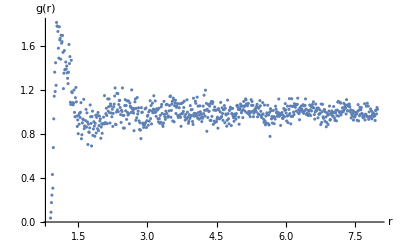

```mathematica
ListPlot[ calcGr[coordList16,16.,0.01],
PlotRange->All,AxesLabel->{"r","g(r)"}]
```

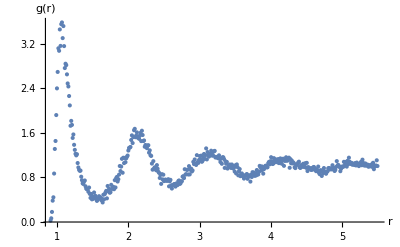

```mathematica
ListPlot[ calcGr[coordList11,11.,0.01],
PlotRange->All,AxesLabel->{"r","g(r)"}]
```

Erratum p. 367 (first printing):  The data supplied in the first line of code displays the L=11 case, but should display the L=9 case.

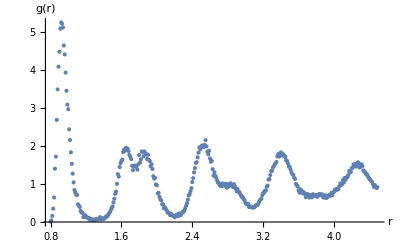

```mathematica
ListPlot[ calcGr[coordList9,9.,0.01],
PlotRange->All,AxesLabel->{"r","g(r)"}]
```